```mathematica
(*model function definition and residual function definition for Nminimize~~alternative is to use NonlinearModelFit*)
f[x_?NumericQ,c_?NumericQ,ka_?NumericQ, k2_?NumericQ]:= Module[{},
Return[c*(-Exp[-ka * x] + Exp[-k2 * x])]]
tracerFunc=c*(-Exp[-ka * x] + Exp[-k2 * x]);
residual[c_,ka_,k2_,data_]:=Module[{},
Return[Plus@@(Table[((f[x,c,ka,k2]/.x-> data[[i,1]]) - data[[i,2]])^2,{i,Length[data]}])]
]
```

```mathematica
names={"LFAL","HFSAL","LFDR","HFSDR"};
ages={"_6months","_12months","_18months","_24months"};
```

```mathematica
all c cohort plots2={};
Table[
nameCount=i;
ageCount=j;
name group=names[[nameCount]]<>ages[[ageCount]];
(*obtaining the data*)
data tab = Import[NotebookDirectory[]<>"LabelledGlucose.xlsx",{"Data",name group}];
times = Select[data tab[[2;;,1]],#!= ""&];
averages = Select[data tab[[2;;,2]],#!= ""&];
std devs = Table[StandardDeviation[Select[data tab[[i,3;;]],#!=""&]],{i,2,10}];
(*constructing lists to contain the parameters/outputs of interest for each fit*)
c Vector = {};
ka Vector = {};
k2 Vector = {};
aic Vector = {};
(*use synthetic variable to specify if synthetic or actual data should be used
real means are used to determine best C for this treatment group*)
synthetic = False;
If[synthetic,
y values = Table[RandomVariate[NormalDistribution[averages[[i]],std devs[[i]]]],{i,Length[times]}],y values = averages];
(*initial parameter guess*)
Table[
c =0.01*i;
ka  = 0.1;
k2  = 0.01;
data to fit = Table[{times[[i]],y values[[i]]},{i,Length[times]}];
(*max boundary for ka is applied as 1*)
result = NonlinearModelFit[data to fit,{c (ⅇ^(-k2 x)-ⅇ^(-ka x)),c==c &&1>=ka>=0&&k2>=0},{{c},{ka, ka },{k2,k2 }},x,MaxIterations->1000];
show fit = False;
If[show fit, Show[
ListPlot[data to fit],
Plot[result//Normal,{x,0,120},PlotStyle->Green]
,PlotRange-> Full]];
AppendTo[c Vector,c ];
AppendTo[ka Vector,ka/.result["BestFitParameters"]];
AppendTo[k2 Vector,k2/.result["BestFitParameters"]];
(*Quiet is included here to avoid General errors of small numbers and related precision loss as well as FittedModel warning about AIC assuming an unconstrained model*)
Quiet[AppendTo[aic Vector,result["AIC"]]];,{i,1,1000}];
min aic=Min[aic Vector];
min for plotRange=Floor[min aic,5];

cPlotdata = Table[{c Vector[[i]],aic Vector[[i]]},{i,Length[aic Vector]}];
c lowestAIC = c Vector[[Position[aic Vector,Min[aic Vector]][[1,1]]]];
cohort c plot=ListPlot[cPlotdata,Frame->True,PlotStyle->Black,FrameLabel->{"C","AIC"},LabelStyle->Bold,PlotLabel->"Best C for "<>ToString[name group]<>": "<>ToString[c lowestAIC],PlotRange->{{0,12},{0,min for plotRange}},ImageSize->Medium];
AppendTo[all c cohort plots2,cohort c plot];
,{i,Length[names]},{j,Length[ages]}];
```

```mathematica
GraphicsGrid[Partition[all c cohort plots2,4],ImageSize->1200];
```

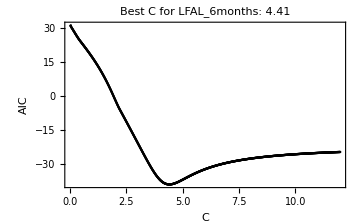
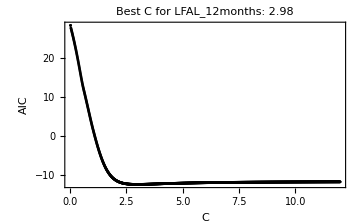
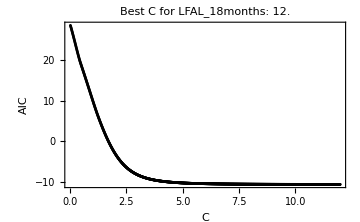
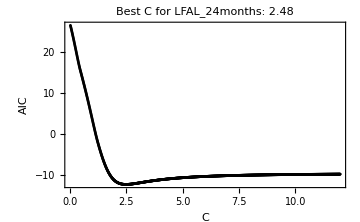
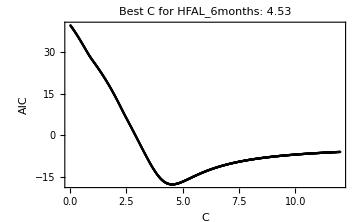
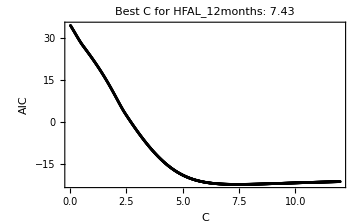
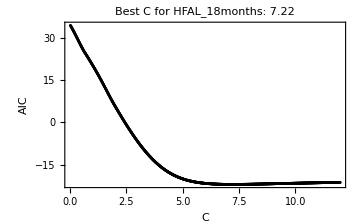
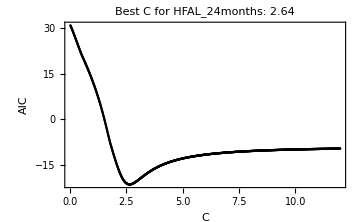
| 4 Months | 9 Months | 15 Months | 21 Months
LFAL | -Graphics- | -Graphics- | -Graphics- | -Graphics-
HFAL | -Graphics- | -Graphics- | -Graphics- | -Graphics-
LFCR | -Graphics- | -Graphics- | -Graphics- | -Graphics-
HFCR | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
xlabels=Text[Style[#,Larger,Bold,FontSize->15]]&/@{"","4 Months","9 Months","15 Months","21 Months"};
ylabels=Text[Style[#,Larger,Bold,FontSize->15]]&/@{"LFAL","HFSAL","LFDR","HFSDR"};
grouped cScanPlots=Grid[Join[{xlabels},Transpose[Join[{ylabels},Transpose[Partition[Table[Show[all c cohort plots[[i]],ImageSize->Medium,ImagePadding->{{20,10},{15,10}}],{i,Length[all c cohort plots]}],4]]]]]]
```

```mathematica
Export[NotebookDirectory[]<>"All cohort c param scan.jpg",grouped cScanPlots]
```

```mathematica
(*declare 1 cohort at a time to proceed with workflow*)
nameCount=2;
ageCount=1;
name group=names[[nameCount]]<>ages[[ageCount]];
data tab = Import[NotebookDirectory[]<>"LabelledGlucose.xlsx",{"Data",name group}];
times = Select[data tab[[2;;,1]],#!= ""&];
averages = Select[data tab[[2;;,2]],#!= ""&];
std devs = Table[StandardDeviation[Select[data tab[[i,3;;]],#!=""&]],{i,2,10}];
```

```mathematica
name group
```

```mathematica
(*now to perform fits on synthetic data*)
(*reconstructing lists to contain the parameters/outputs of interest for each fit*)
c Vector = {};
ka Vector = {};
k2 Vector = {};
aic Vector = {};
(*Declare range of C values to test, as well as the number of fits to perform (start with more C values and lower number of fits then decrease the number of C values and increase the number of synthetic fits as the you get closer to identifying the optimal C per cohort)*)
c range = Range[4.4,4.6,0.1];
synthetic2 = True;

For[j=1,j<=Length[c range],j++,ka subVector = {};k2 subVector = {};aic subVector = {};c subVector = {};
For[i=1,i<=20000,i++,If[synthetic2,y values = Table[RandomVariate[NormalDistribution[averages[[l]],std devs[[l]]]],{l,Length[times]}],y values = averages];(*initial parameter guesses*)
c  = c range[[j]];ka  = 0.1;k2  = 0.01;data to fit = Table[{times[[k]],y values[[k]]},{k,Length[times]}];
result = NonlinearModelFit[data to fit,{c (ⅇ^(-k2 x)-ⅇ^(-ka x)),c==c &&1>=ka>=0&&k2>=0},{{c},{ka, ka },{k2,k2 }},x];
AppendTo[ka subVector,ka/.result["BestFitParameters"]];AppendTo[k2 subVector,k2/.result["BestFitParameters"]];
AppendTo[c subVector,c/.result["BestFitParameters"]];Quiet[AppendTo[aic subVector,result["AIC"]]]
];
AppendTo[c Vector,c subVector];AppendTo[ka Vector,ka subVector];AppendTo[k2 Vector,k2 subVector];
Quiet[AppendTo[aic Vector,aic subVector]];
Print["Finished c:"<>ToString[c range[[j]]]]
]
```

```mathematica
pairedSpearC=Table[{c range[[i]],SpearmanRho[ka Vector[[i]],k2 Vector[[i]]]},{i,Length[c range]}]
```

```mathematica
spearFit=LinearModelFit[pairedSpearC,x,x]
```

```mathematica
Show[ListPlot[pairedSpearC],Plot[spearFit//Normal,{x,c range[[1]],c range[[-1]]}]]
```

```mathematica
Reduce[(spearFit//Normal)==0.5]
```

```mathematica
synthetic = True;
c Vector = {};
ka Vector = {};
k2 Vector = {};
aic Vector = {};
Table[
If[synthetic,y values = Table[RandomVariate[NormalDistribution[averages[[l]],std devs[[l]]]],{l,Length[times]}],y values = averages];
(*Declare the c value to use for this cohort (based on the C parameter scan done initially as well as the correlation between ka and k2 at different C values) *)
c =4.53;
ka  = 0.1;
k2  = 0.01;
data to fit = Table[{times[[i]],y values[[i]]},{i,Length[times]}];
(*max boundary for ka is applied as 1*)
result = NonlinearModelFit[data to fit,{c (ⅇ^(-k2 x)-ⅇ^(-ka x)),c==c &&1>=ka>=0&&k2>=0},{{c},{ka, ka },{k2,k2 }},x,MaxIterations->1000];
show fit = False;
If[show fit, Show[
ListPlot[data to fit],
Plot[result//Normal,{x,0,120},PlotStyle->Green]
,PlotRange-> Full]];
AppendTo[c Vector,c/.result["BestFitParameters"]];
AppendTo[ka Vector,ka/.result["BestFitParameters"]];
AppendTo[k2 Vector,k2/.result["BestFitParameters"]];
(*Quiet is included here to avoid General errors of small numbers and related precision loss as well as FittedModel warning about AIC assuming an unconstrained model*)
Quiet[AppendTo[aic Vector,result["AIC"]]];
If[Mod[i,20000]==0,Print[i]],{i,1,100000}];
```

```mathematica
Median[ka Vector]
Median[k2 Vector]
```

```mathematica
filtered ka sub 0 05 = Select[ka Vector,#<=0.5&];
filtered k2 sub 0 05=Select[k2 Vector,#<=0.5&];
```

```mathematica
Quantile[ka Vector,{0.025,0.5,0.975}]
Quantile[k2 Vector,{0.025,0.5,0.975}]
```

```mathematica
ka Vector//Length
filtered ka sub 0 05//Length
```

```mathematica
k2 Vector//Length
filtered k2 sub 0 05//Length
```

```mathematica
Quantile[filtered ka sub 0 05,{0.025,0.5,0.975}]
Quantile[filtered k2 sub 0 05,{0.025,0.5,0.975}]
```